## Initialization

```mathematica
SetDirectory[NotebookDirectory[]]; 
Import["../src/hlt_construct.wl"]; 
Import["../src/wilson_loops.wl"];
```

### Plotting

```mathematica
t = 0.01;  
kticks =  {{0,"0", {0.,t}}, {π/2, "π/2", {0.,t}}, {π, "π", {0.,t}}, {-π/2, "-π/2", {0.,t}}, {-π, "-π", {0.,t}}};
```

## Chern insulator

#### Model definitions

```mathematica
ClearAll[ kx,ky,m, H]; 
H[{kx_, ky_}] := Sin[kx] σ1 + Sin[ky] σ2 + (2 - m -Cos[kx] - Cos[ky]) σ3;
```

```mathematica
H[{kx,ky}] // MatrixForm
```

(2-m-Cos[kx]-Cos[ky] | Sin[kx]-ⅈ Sin[ky]
Sin[kx]+ⅈ Sin[ky] | -2+m+Cos[kx]+Cos[ky])

```mathematica
m = 1.0; kstep = 0.025π; 
εlist = Flatten[Table[Chop[Sort[Eigenvalues[H[{kx,ky}]]]], {kx, -π,π,kstep}, {ky,-π,π,kstep}],  {{3}, {1},{2}}]; 
ListPlot3D[εlist, PlotStyle->Opacity[0.75]]
```

-Graphics3D-

#### Wilson loops and the Chern number

```mathematica
m = 1;      (* Set the mass parameter *) 

Noc = 1;      (* Number of occupied bands *) 
Npts = 20;  (* Number of discretization points for the computation of Wilson loop. *) 

kstep = 0.02π; 

(* Wilson loops and polarization along x *) 
WlistX = Table[ComputeWilson[H[{#,k}]& ,Noc, Npts], {k, -π,π,kstep}]⟦All,1,1⟧;
polX = Mod[1/(2π)Arg[WlistX],1]; 

(* Wilson loops and polarization along y *) 
WlistY = Table[ComputeWilson[H[{k,#}]& ,Noc, Npts], {k, -π,π,kstep}]⟦All,1,1⟧; 
polY = Mod[1/(2π)Arg[WlistY],1]; 

(* Chern number = Winding of the Wilson loops *) 
Print["Chern number of the occupied bands = ", CalculateChern[H, Noc, Npts]];
```

Chern number of the occupied bands = 1.

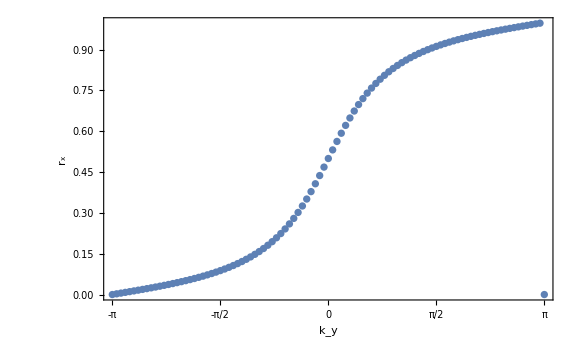

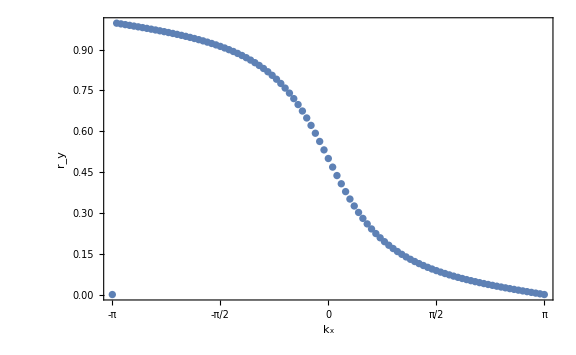

```mathematica
(* Plot Subscript[r, x](Subscript[k, y]) *) 
ListPlot[polX, DataRange-> {-π,π}, Axes-> False, PlotRangePadding->None, 
Frame-> True, FrameStyle->Directive[Black, Thick],FrameTicks->{{ Automatic, None},{kticks,None}}, 
FrameLabel->{{ "r_x", None}, {"k_y", None}},FrameTicksStyle->Directive[Black, 22,FontFamily-> "Latin Modern Roman"], 
LabelStyle-> {{Black, FontSize-> 22,  FontFamily-> "Latin Modern Roman"}}, ImageSize->Large]

(* Plot Subscript[r, y](Subscript[k, x]) *) 
ListPlot[polY, DataRange-> {-π,π}, Axes-> False, PlotRangePadding->None, 
Frame-> True, FrameStyle->Directive[Black, Thick],FrameTicks->{{ Automatic, None},{kticks,None}}, 
FrameLabel->{{ "r_y", None}, {"k_x", None}},FrameTicksStyle->Directive[Black, 22,FontFamily-> "Latin Modern Roman"], 
LabelStyle-> {{Black, FontSize-> 22,  FontFamily-> "Latin Modern Roman"}}, ImageSize->Large]
```

#### Exact diagonalization on a cylinder

```mathematica
(* Construct the real space Hamiltonian for OBC along x. *) 
m = 0.8;      (* Set the mass parameter *) 

Htemp=H[{ⅈ Log[a],ky}]; 
J=SeriesCoefficient[Htemp, {a,0,1}];   (* Extract coefficient of ⅇ^(-ⅈ kx) *) 
M=SeriesCoefficient[Htemp, {a,0,0}];

len=40; 
Hrealsp = ConstructRealSpaceHlt[J,M,len]; 

(* Numerically compute the spectrum of the real space Hamiltonian. *) 
kymin = -π; kymax = π;  
kstep = 0.02 π; 
εlist = Table[Sort[Chop[Eigenvalues[N[Hrealsp]]]],{ky,-kymax,kymax,kstep} ]ᵀ;
```

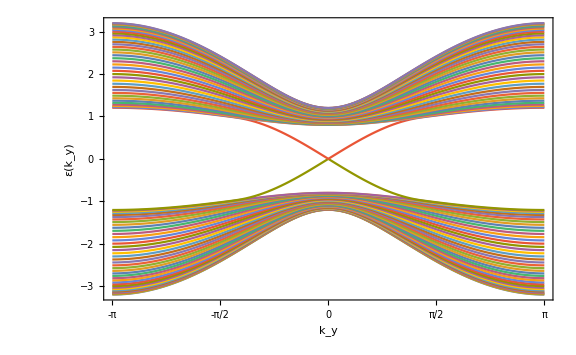

```mathematica
ListLinePlot[εlist, DataRange-> {-π,π}, PlotRangePadding->{None, Automatic}, 
Frame-> True, FrameStyle->Directive[Black, Thick],FrameTicks->{{ Automatic, None},{kticks,None}}, 
FrameLabel->{{ "ε(k_y)", None}, {"k_y", None}},FrameTicksStyle->Directive[Black, 22,FontFamily-> "Latin Modern Roman"], 
LabelStyle-> {{Black, FontSize-> 22,  FontFamily-> "Latin Modern Roman"}}, ImageSize->Large]
```

## BBH model (“quadrupole insulator”)

#### Model definitions

```mathematica
ClearAll[γ,λ,δ, H,  kx, ky]; 
H[{kx_,ky_}] := ({{δ, γ+λ ⅇ^(-ⅈ kx), 0, γ+ λ ⅇ^(ⅈ ky)}, {γ+λ ⅇ^(ⅈ kx), δ, -γ- λ ⅇ^(ⅈ ky), 0}, {0, -γ- λ ⅇ^(-ⅈ ky), -δ, γ+λ ⅇ^(ⅈ kx)}, {γ+ λ ⅇ^(-ⅈ ky), 0, γ+λ ⅇ^(-ⅈ kx), -δ}});
```

```mathematica
γ = 1; λ = 2; δ = 0.5; 
kstep = 0.025π; 
εlist = Flatten[Table[Chop[Sort[Eigenvalues[H[{kx,ky}]]]], {kx, -π,π,kstep}, {ky,-π,π,kstep}],  {{3}, {1},{2}}]; 
ListPlot3D[εlist, PlotStyle->Opacity[0.75]]
```

-Graphics3D-

#### Wilson loops and the Chern number

```mathematica
γ = 1; λ = 2; δ=0;       (* Set the lattice parameters *) 

Noc = 2;      (* Number of occupied bands *) 
Npts = 20;  (* Number of discretization points for the computation of Wilson loop. *) 

kstep = 0.02π; 

(* Function to compute the polarization from the eigenvalues of the Wilson loop  *) 
ComputeWPol[Wloop_] := Sort[Mod[1/(2π)Arg[Eigenvalues[Wloop]],1]]; 

(* Wilson loops and polarization along x *) 
WlistX = Table[ComputeWilson[H[{#,k}]& ,Noc, Npts], {k, -π,π,kstep}];
polX = ComputeWPol/@ WlistX; 

(* Wilson loops and polarization along y *) 
WlistY = Table[ComputeWilson[H[{k,#}]& ,Noc, Npts], {k, -π,π,kstep}]; 
polY = ComputeWPol/@ WlistY; 

(* Chern number = Winding of the Wilson loops *) 
Print["Chern number of the occupied bands = ", CalculateChern[H, Noc, Npts]];
```

Chern number of the occupied bands = 0

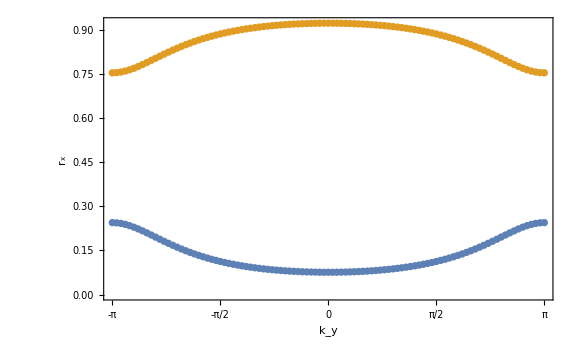

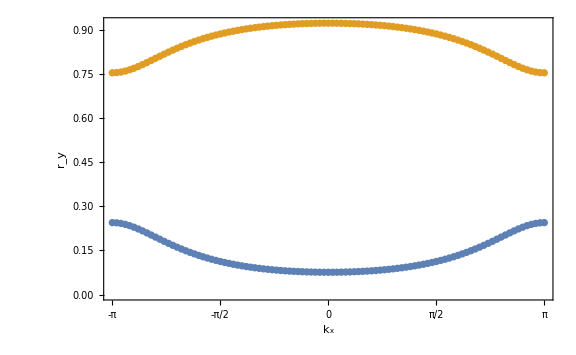

```mathematica
(* Plot Subscript[r, x](Subscript[k, y]) *) 
ListPlot[polXᵀ, DataRange-> {-π,π}, Axes-> False, PlotRangePadding->None, 
Frame-> True, FrameStyle->Directive[Black, Thick],FrameTicks->{{ Automatic, None},{kticks,None}}, 
FrameLabel->{{ "r_x", None}, {"k_y", None}},FrameTicksStyle->Directive[Black, 22,FontFamily-> "Latin Modern Roman"], 
LabelStyle-> {{Black, FontSize-> 22,  FontFamily-> "Latin Modern Roman"}}, ImageSize->Large]

(* Plot Subscript[r, y](Subscript[k, x]) *) 
ListPlot[polYᵀ, DataRange-> {-π,π}, Axes-> False, PlotRangePadding->None, 
Frame-> True, FrameStyle->Directive[Black, Thick],FrameTicks->{{ Automatic, None},{kticks,None}}, 
FrameLabel->{{ "r_y", None}, {"k_x", None}},FrameTicksStyle->Directive[Black, 22,FontFamily-> "Latin Modern Roman"], 
LabelStyle-> {{Black, FontSize-> 22,  FontFamily-> "Latin Modern Roman"}}, ImageSize->Large]
```

#### Exact diagonalization on a cylinder

```mathematica
(* Construct the real space Hamiltonian for OBC along x. *) 
γ = 1; λ = 2; δ=0;       (* Set the lattice parameters *) 

Htemp=H[{ⅈ Log[a],ky}]; 
J=SeriesCoefficient[Htemp, {a,0,1}];   (* Extract coefficient of ⅇ^(-ⅈ kx) *) 
M=SeriesCoefficient[Htemp, {a,0,0}];

len=40; 
Hrealsp = ConstructRealSpaceHlt[J,M,len]; 

(* Numerically compute the spectrum of the real space Hamiltonian. *) 
kymin = -π; kymax = π;  
kstep = 0.02 π; 
εlist = Table[Sort[Chop[Eigenvalues[N[Hrealsp]]]],{ky,-kymax,kymax,kstep} ]ᵀ;
```

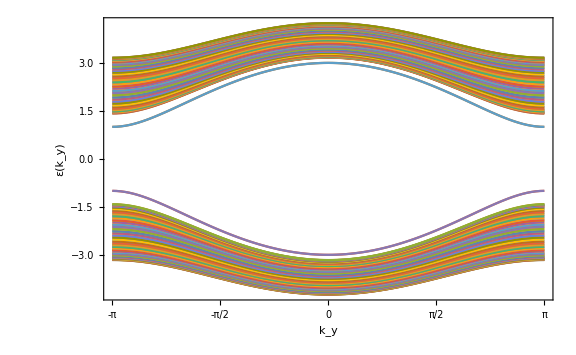

```mathematica
ListLinePlot[εlist, DataRange-> {-π,π}, PlotRangePadding->{None, Automatic}, 
Frame-> True, FrameStyle->Directive[Black, Thick],FrameTicks->{{ Automatic, None},{kticks,None}}, 
FrameLabel->{{ "ε(k_y)", None}, {"k_y", None}},FrameTicksStyle->Directive[Black, 22,FontFamily-> "Latin Modern Roman"], 
LabelStyle-> {{Black, FontSize-> 22,  FontFamily-> "Latin Modern Roman"}}, ImageSize->Large]
```

#### Exact diagonalization on a square: corner modes